```mathematica
BPolynomial[n_,i_,a_,b_,x_]:=Binomial[n,i]((x-a)^i (b-x)^(n-i))/(b-a)^n ;
SortEigensystem[eigsys_]:=Transpose[Sort[Transpose[eigsys]]];
psi[1,0]=2 Z^(3/2) x ⅇ^(-Z x);
psi[2,0]=1/(√2) Z^(3/2) x ⅇ^(-Z x/2) (1-1/2 Z x);
psi[2,1]=1/(2 √6) Z^(5/2) x^2 ⅇ^(-Z x/2);
psi[3,0]=2/(3 √3) Z^(3/2) x ⅇ^(-Z x/3) (1-2/3 Z x+2/27 Z^2 x^2);
psi[3,1]=8/(27 √6) Z^(5/2) x^2 ⅇ^(-Z x/3) (1-1/6 Z x);
psi[3,2]=4/(81 √30) Z^(7/2) x^3 ⅇ^(-Z x/3);
```

```mathematica
P[k_,x_]:=BPolynomial[n+1,k,0,R,x];
```

```mathematica
A[i_,j_,R_]:=NIntegrate[D[P[i,x],x] D[P[j,x],x]+2P[i,x](-Z/x+(l (l+1))/(2 x^2))P[j,x],{x,0,R},Method->"DoubleExponential",MaxRecursion->200];
B[i_,j_,R_]:=NIntegrate[P[i,x] P[j,x],{x,0,R},Method->"DoubleExponential",MaxRecursion->200];
```

```mathematica
n=3;Z=83; R=30/Z; l=0;
```

```mathematica
matA=Table[A[i,j,R],{i,1,n},{j,1,n}];
```

```mathematica
matB=Table[ B[i,j,R],{i,1,n},{j,1,n}];
```

```mathematica
eigensystem=Eigensystem[{matA,matB}];
```

```mathematica
sortedeigensystem=SortEigensystem[eigensystem];
```

```mathematica
norms=Table[Solve[const[k]^2 Sum[sortedeigensystem[[2,k,i]]  B[i,j,R] sortedeigensystem[[2,k,j]],{i,1,n},{j,1,n}]==1,const[k]],{k,1,n}];
```

```mathematica
For[i=1,i≤n,i++,y[n,i]=∑_(j=1)^n const[i] sortedeigensystem[[2,i,j]] P[j,x]/.norms[[i,2]];]
```

```mathematica
For[i=1,i≤n,i++,If[(D[y[n,i],x]/.x->0)>0,y[n,i]=(1) y[n,i];,y[n,i]=(-1) y[n,i];]; Print["y",{n,i}," = ",y[n,i]]]
```

y{3,1} = 2894.16 (30/83-x)^3 x-4200.5 (30/83-x)^2 x^2+1012.84 (30/83-x) x^3

y{3,2} = 955.345 (30/83-x)^3 x-4364.22 (30/83-x)^2 x^2+672.423 (30/83-x) x^3

y{3,3} = 826.804 (30/83-x)^3 x-4376.64 (30/83-x)^2 x^2+2914.52 (30/83-x) x^3

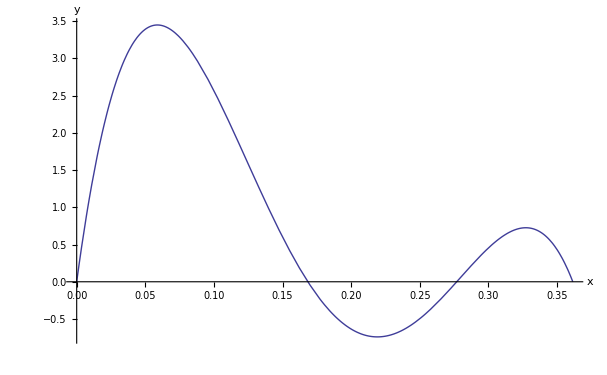

```mathematica
Plot[Table[y[n,1],{i,1,1}],{x,0,R},AxesLabel->{"x","y"}]
```

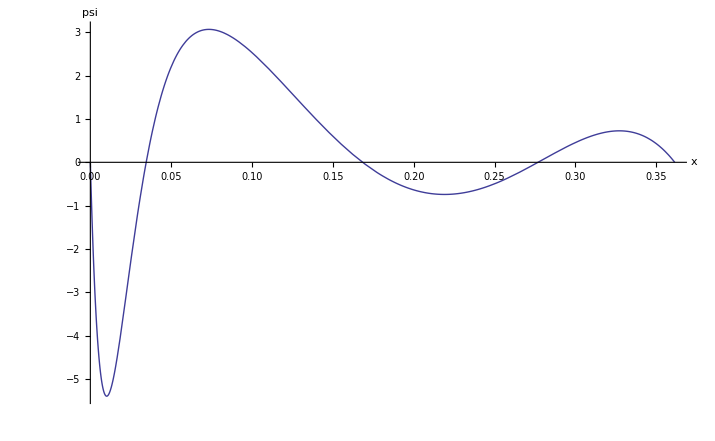

```mathematica
Plot[y[n,1]-psi[1,0],{x,0,R},AxesLabel->{"x","psi"}]
```

```mathematica
residual[n]=√NIntegrate[(y[n,1]-psi[1,0])^2,{x,0,R}]
```

1.04221

```mathematica
energies=sortedeigensystem[[1]]/2
```

{-1322.48,-403.7,-95.5766}

```mathematica
residuals=Table[residual[i],{i,3,18,3}]
```

{1.08621,0.223399,0.0139096,0.000347564,2.93584×10^-6,9.30601×10^-9}

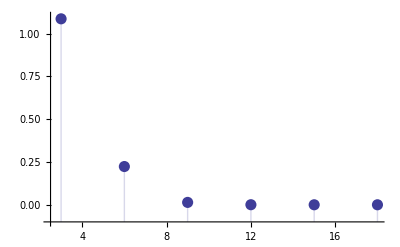

```mathematica
DiscretePlot[residual[i],{i,3,18,3},PlotRange->{{2.5,18},{-0.1,1.1}},PlotStyle->PointSize[0.02],AxesOrigin->{2.5,-0.1}]
```

```mathematica
Clear[y]
```